```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/silvestre_parameters.nb"];
NotebookEvaluate["modules/expVal_delta.nb"];
NotebookEvaluate["modules/find_minimum.nb"];
On[Assert]
```

```mathematica
(* INITIALISE HYPERPARAMETERS AND OBTAIN LOWEST LYING STATE *)
(**** !!!TUNABLE PARAMETERS!!! ****)
(**** !!!TUNABLE PARAMETERS!!! ****)
J=1/2;(* Total angular momentum J = Λ + S *)
P=+1;(* Parity P=(-1)^(Subscript[l, ρ]+Subscript[l, λ]) *)
Isospin=1;(* Isospin *)
γMax=10;(* Maximum energy of considered basis states (2n+l+2N+L), use this to control Subscript[N, Q] *)
Λ=0;(* Total orbital angular momentum Λ = Subscript[l, ρ] + Subscript[l, λ] *)
m1=bq;(* mass of quark 1 *)
m2=bq;(* mass of quark 2 *)
m3=uq;(* mass of quark 3 *)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)
(**** !!!END OF TUNABLE PARAMETERS!!! ****)

(* Choose to project depending if m1=m2 or m1≠m2, True and False, respectively *)
If[m1==m2,project=True,project=False];

(* Obtain projector matrix *)
projector=Projector[J,P,Λ,γMax,Isospin];

(* Calculate generalised transformation matrices *)
t1=tMatrix[J,P,Λ,γMax,m1,m2,m3,1];
t2=tMatrix[J,P,Λ,γMax,m1,m2,m3,2];

(* Obtain size of basis from size of talmi matrices (Subscript[N, Q]) *)
size=Dimensions[t1][[1]];

(* If projector has been applied, find position of first non-zero eigenvalue, if not applied then it's 1 *)
If[project==True,firstNonZero=size-Total[Diagonal[projector]]+1,firstNonZero=1];
```

0.5

{0.488491,10.1957}

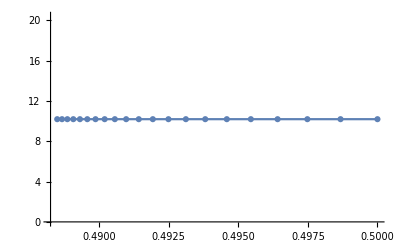

{{0.5,10.1957},{0.498673,10.1957},{0.497481,10.1957},{0.496411,10.1957},{0.495449,10.1957},{0.494586,10.1957},{0.493811,10.1957},{0.493114,10.1957},{0.492488,10.1957},{0.491927,10.1957},{0.491422,10.1957},{0.490969,10.1957},{0.490561,10.1957},{0.490196,10.1957},{0.489867,10.1957},{0.489572,10.1957},{0.489307,10.1957},{0.489069,10.1957},{0.488855,10.1957},{0.488663,10.1957},{0.488491,10.1957}}

```mathematica
min=findMinimum[1,20];
Print[{min[[1]],min[[2]]}]
data=min[[3]];
ListPlot[data,Joined->True,PlotMarkers->Automatic]
data
```

```mathematica
Eigenvalues[Hb[J,P,Isospin,Λ,γMax,0.55,m1,m2,m3,project]]
```

{14.811,14.8076,14.7141,14.6949,14.6832,14.6498,14.5665,14.5578,14.4931,14.4594,14.4482,14.4452,14.3961,14.3228,14.2476,14.0683,14.0408,14.0033,13.9596,13.9031,13.8541,13.3429,13.3065,13.2902,13.1642,13.1606,13.1472,13.097,13.0128,12.9741,12.9279,12.9231,12.8858,12.841,12.7838,12.7334,12.2685,12.2241,12.223,12.1214,12.0893,12.0804,12.0559,11.9655,11.9265,11.8138,11.5219,11.5001,11.4771,11.3323,11.315,11.0805,10.9,10.8871,10.5724,10.1959,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}